```mathematica
(*Import the video and set videoFrames to the image list of frames *)

filename="D:\\OU Fall 2023\\Advnaced Lab lets GO!\\Cavendish\\runs\\run1.MOV";
frames=Import[filename,"ImageList"];
```

```mathematica
(*Get video dimensions for cropping*)
Manipulate[ImageTake[frames[[1]],{a,b},{c,d}],{a,1,1080},{b,2,1080},{c,1,1920},{d,2,1920}]
```

Part::partd: Part specification frames[[1]] is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of frames[[1]].

Part::partd: Part specification frames[[1]] is longer than depth of object.

ImageTake::imginv: Expecting an image or graphics instead of frames[[1]].

```mathematica
(*Cropping the image *)
length=Length[frames];
ymin=230;
ymax=370;
xmin=1;
xmax=1920;
croppedFrames=Table[ImageTake[frames[[i]],{ymin,ymax},{xmin,xmax}],{i,length}];
```

```mathematica
(*Show crop*)
```

```mathematica
croppedFrames[[1]]
```

-Graphics-

```mathematica
length
```

714

```mathematica
(*Use binarize to create a binary image set*)
```

```mathematica
binarizedFrames=Table[Binarize[croppedFrames[[i]],.5],{i,length}];
newBinarizedFrames=Table[DeleteSmallComponents[binarizedFrames[[i]]],{i,length}];
```

```mathematica
(*Get coordinates for the pixels*)
```

```mathematica
help=Table[ComponentMeasurements[newBinarizedFrames[[i]],"Centroid"],{i,length}]//Values;
xvals=Flatten[help[[;;,;;,1]]];
yvals=Flatten[help[[;;,;;,2]]];
```

```mathematica
(*Plot*)
```

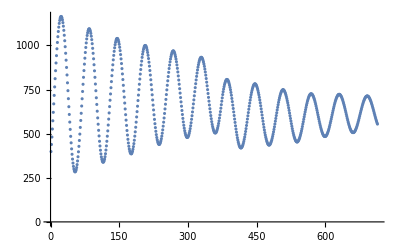

```mathematica
ListPlot[Transpose[xvals]]
```

```mathematica
mylist=Transpose@{xvals,yvals}

Export["D:\\OU Fall 2023\\Advnaced Lab lets GO!\\Cavendish\\runs\\run1xvals.csv",mylist,"CSV"]
```

{{398.5,54.6667},{438.7,54.1},{480.833,53.8333},{526.3,53.9},{572.929,53.3571},{620.786,53.0714},{668.833,52.6111},{716.786,52.0714},{764.875,51.75},{811.5,51.2143},{856.7,50.9},{900.375,51.375},{941.955,51.6818},{980.786,51.0714},{1016.63,51.375},{1049.33,51.3333},{1078.79,51.5},{1103.5,51.5},{1124.79,52.3571},{1141.5,52.2143},{1153.79,52.3571},{1161.,52.},{1164.,52.},{1162.3,52.1},{1155.9,51.7},{1144.7,52.1},{1129.1,51.9},{1109.,51.5},{1085.38,51.625},{1057.5,51.5},{1026.5,51.2143},{992.611,51.1667},{955.5,51.},{916.375,51.375},{875.125,51.75},{832.5,51.5},{788.,52.},{743.5,52.},{698.214,52.3571},{652.667,53.1667},{608.786,53.5},{565.5,53.75},{524.167,54.1667},{484.75,54.25},{448.,54.5},{413.7,55.1},{383.147,55.5},{355.833,55.8333},{333.3,55.9},{314.5,55.5},{299.833,55.8333},{289.5,56.},{284.167,56.1667},{283.833,55.8333},{287.833,55.8333},{295.5,56.},{307.833,55.8333},{324.5,56.},{345.3,55.9},{369.,56.},{397.167,55.1667},{428.,55.},{461.3,54.9},{497.5,54.25},{535.3,53.9},{574.7,54.1},{615.333,53.6667},{656.5,53.3333},{697.667,52.8333},{738.929,52.3571},{779.8,52.3},{819.214,52.3571},{857.333,51.6667},{893.8,51.9},{927.6,51.7},{959.833,51.3889},{988.375,51.625},{1014.,52.},{1036.67,51.6667},{1056.21,51.5},{1071.21,51.6429},{1082.61,52.1667},{1090.25,51.875},{1094.,52.5},{1093.63,52.375},{1089.,51.5},{1080.5,52.},{1068.2,51.9},{1052.21,51.5},{1032.64,51.9286},{1009.79,51.9286},{983.5,51.2143},{955.25,51.5},{924.167,51.7222},{890.5,51.5},{855.929,51.3571},{819.214,52.3571},{781.125,52.125},{743.167,52.6667},{703.3,53.3},{665.5,53.},{627.25,53.25},{589.25,53.75},{553.5,54.3333},{518.833,54.8333},{487.,54.5},{456.7,55.1},{430.167,55.1667},{406.167,55.1667},{385.3,55.7},{368.167,56.1667},{355.,56.},{345.5,56.},{339.5,56.},{338.167,56.1667},{340.167,56.1667},{346.,56.5},{355.833,55.8333},{369.333,56.5},{386.214,55.9286},{407.167,55.1667},{430.5,55.5},{456.7,55.1},{485.5,55.},{515.5,54.7857},{548.7,54.1},{582.5,54.},{617.333,53.6667},{653.3,53.5},{689.357,53.2143},{724.955,53.0455},{760.227,52.6818},{794.944,52.3889},{828.5,52.2143},{860.2,52.2},{890.,52.},{918.056,52.0556},{943.5,51.8333},{966.389,51.8333},{986.5,52.},{1003.9,51.7},{1017.39,52.1667},{1028.5,52.2143},{1035.64,51.9286},{1039.3,52.},{1039.39,52.1667},{1035.9,51.7},{1029.36,52.2143},{1019.5,52.},{1006.3,51.9},{989.5,52.},{970.333,51.8333},{948.045,51.8636},{923.625,51.625},{897.167,51.7222},{868.5,51.7857},{838.333,52.3333},{806.5,52.},{773.944,52.7222},{740.5,53.},{707.,53.},{673.357,53.2143},{639.833,53.6111},{607.5,53.7857},{576.7,54.1},{546.7,54.1},{517.75,55.25},{492.,55.},{468.,55.},{447.167,55.1667},{428.5,56.},{413.333,55.6667},{401.3,55.9},{392.833,55.8333},{387.7,56.1},{385.654,55.9615},{386.333,56.},{392.,56.},{400.,56.},{411.3,55.5},{426.5,55.25},{443.5,55.25},{462.7,55.1},{485.833,54.8333},{510.167,55.1667},{536.25,54.75},{565.,54.1667},{594.5,54.},{624.7,54.1},{655.5,54.},{687.5,53.25},{718.5,53.},{749.389,53.1667},{779.833,53.},{809.3,52.1},{837.5,52.},{863.375,52.375},{888.5,52.3},{910.864,52.1364},{932.192,52.2692},{950.,52.0833},{964.9,52.1},{977.875,52.125},{987.9,51.7},{995.167,52.},{998.9,52.3},{999.643,52.0714},{997.611,52.1667},{992.611,52.1667},{984.625,52.},{973.333,51.6667},{960.071,51.7857},{943.773,52.0455},{925.625,52.375},{904.682,52.0455},{882.5,52.2143},{857.7,52.1},{832.,52.},{805.333,52.3333},{777.5,52.5},{749.,53.3},{720.214,53.0714},{690.75,53.5},{661.833,53.8333},{634.3,53.9},{607.,54.},{580.75,54.5},{556.5,54.3333},{534.3,54.5},{513.333,54.6667},{494.5,55.},{478.3,54.9},{465.167,55.1667},{454.,55.},{446.,55.5},{441.25,55.75},{438.722,55.7222},{439.3,56.2},{443.5,55.25},{449.7,55.1},{459.3,55.1},{471.167,55.1667},{485.833,54.8333},{502.5,55.},{521.5,54.5},{542.5,54.25},{564.929,54.3571},{588.7,54.1},{614.333,53.6667},{640.,53.625},{666.786,53.3571},{694.,53.1667},{721.5,52.7857},{748.,53.},{774.,52.5},{799.375,52.375},{823.667,52.5},{847.3,51.9},{869.071,52.2143},{888.5,52.3},{906.833,51.9444},{922.833,52.0556},{936.5,52.},{947.75,52.1667},{957.,51.5},{963.667,51.6667},{967.357,52.2143},{969.167,51.8333},{967.5,52.},{963.214,51.6429},{956.5,52.},{947.75,52.1667},{936.25,52.125},{922.75,51.875},{907.389,52.1667},{889.5,52.},{870.167,51.6111},{849.5,52.2143},{827.071,52.5},{803.7,52.1},{779.955,52.8636},{754.833,52.6111},{729.786,52.6429},{704.5,53.},{680.,53.1667},{655.5,53.7857},{631.214,53.5},{608.5,54.},{586.5,54.5},{566.3,54.5},{547.5,54.5},{531.1,54.7},{516.5,54.5},{504.1,54.7},{494.1,54.7},{486.833,54.8333},{481.5,55.},{478.5,55.},{478.5,55.},{481.,55.},{485.833,54.8333},{492.7,55.1},{502.833,54.8333},{514.5,55.},{528.5,54.6667},{544.5,54.5},{561.75,54.5},{581.357,54.2143},{601.5,54.},{623.,54.},{645.667,53.6667},{668.5,53.5},{691.214,53.5},{714.5,53.1667},{737.875,52.75},{760.75,52.75},{783.,52.7},{804.3,51.9},{824.7,52.1},{843.214,51.9286},{860.929,52.2143},{876.75,51.875},{890.667,51.5},{903.167,52.},{913.278,51.9444},{921.375,51.625},{927.25,51.875},{931.115,51.8846},{932.682,52.3182},{931.833,52.0833},{928.5,51.75},{923.,51.5},{915.667,51.6667},{906.,51.75},{894.611,52.1667},{881.214,51.6429},{865.786,52.5},{849.375,52.375},{831.5,52.3333},{812.3,52.5},{791.611,52.7222},{770.875,52.75},{749.389,53.1667},{727.5,53.},{705.5,53.},{684.1,53.3},{662.333,53.6667},{641.3,53.5},{621.357,54.2143},{602.3,53.9},{584.7,54.1},{568.,54.},{552.5,55.3},{539.929,54.7857},{529.25,54.5},{519.5,54.8333},{512.3,54.9},{506.833,54.8333},{504.333,55.},{504.1,54.7},{505.1,54.7},{509.,55.},{515.071,54.7857},{523.,55.},{533.,55.},{544.5,54.25},{557.7,54.1},{572.5,54.5},{588.7,54.1},{606.375,54.},{624.7,54.1},{644.167,53.6667},{664.,53.},{683.9,53.7},{702.667,53.5},{721.375,52.625},{737.786,52.5},{752.5,53.},{766.3,52.5},{778.25,52.75},{787.5,52.5},{795.5,53.},{801.227,52.6818},{805.5,52.5},{807.1,51.7},{806.214,51.9286},{804.,52.},{799.5,52.5},{793.25,52.875},{784.625,52.625},{774.125,52.75},{762.,52.625},{748.8,52.8},{733.5,52.5},{717.5,53.},{699.5,53.3333},{681.5,53.7857},{661.75,54.375},{642.625,53.625},{622.9,53.3},{602.833,54.3333},{582.7,54.1},{563.667,54.5},{544.3,54.9},{526.125,55.25},{508.7,55.1},{492.7,55.1},{477.3,54.9},{464.,55.},{452.,55.},{442.,55.5},{432.833,55.8333},{426.833,55.8333},{421.833,55.8333},{419.75,55.25},{419.,55.5},{420.3,55.5},{424.167,55.1667},{428.5,56.},{435.7,55.7},{444.5,55.8333},{455.5,55.},{467.5,55.},{480.833,54.8333},{495.833,54.8333},{512.167,54.8333},{528.5,55.},{546.333,54.6667},{564.,54.5},{582.7,54.1},{601.,54.},{619.357,54.2143},{638.214,53.9286},{655.833,54.},{673.071,53.9286},{689.786,53.3571},{705.5,53.3},{720.5,52.75},{733.214,52.5},{744.955,52.8636},{755.333,52.6667},{764.,53.},{771.5,52.7857},{776.833,52.7222},{780.136,52.7727},{782.167,52.3333},{781.75,52.25},{779.833,53.},{776.071,52.7857},{770.5,53.3333},{763.5,52.7857},{754.6,53.},{744.5,53.},{732.5,53.},{720.357,52.7857},{705.7,53.1},{690.75,53.5},{674.75,53.5},{658.,54.},{640.5,54.},{623.1,53.7},{605.5,53.7857},{587.5,54.5},{570.5,54.3333},{553.1,55.1},{536.25,54.75},{520.833,54.8333},{506.,55.},{492.5,55.},{480.,54.5},{469.833,54.8333},{459.5,55.3333},{451.833,55.1667},{444.5,55.8333},{439.682,55.9545},{436.7,55.7},{435.5,55.3333},{435.667,55.3333},{437.7,55.5},{442.,55.5},{447.5,55.5},{454.7,55.1},{462.7,55.1},{472.7,55.1},{484.3,54.9},{496.3,54.9},{510.,55.},{524.,55.},{538.833,54.8333},{554.5,54.5},{570.3,54.3},{586.167,54.1667},{602.5,54.},{618.25,53.875},{634.167,53.6667},{649.,53.6667},{663.9,53.3},{677.5,53.5},{690.786,53.3571},{702.,53.},{712.944,53.3889},{722.389,53.1667},{730.278,52.8333},{737.333,52.6667},{742.389,53.1667},{745.722,52.9444},{748.5,52.7857},{749.,53.},{747.944,52.8333},{744.833,53.},{740.5,53.},{734.75,53.125},{728.056,53.3889},{719.667,52.8333},{709.786,53.0714},{698.9,53.3},{687.,53.},{674.833,53.1667},{660.786,53.5},{646.5,54.},{631.75,53.875},{616.5,53.8333},{601.5,54.},{586.167,54.1667},{571.5,54.},{556.7,54.3},{542.,54.5},{528.5,54.5},{515.333,54.6667},{503.5,54.5},{492.7,55.1},{483.,55.},{475.,55.},{467.7,55.1},{461.5,55.3333},{457.7,55.1},{454.5,55.},{452.9,55.3},{453.167,55.1667},{454.7,55.1},{459.,55.1667},{462.5,55.},{469.,54.5},{475.7,55.1},{484.3,54.9},{494.,54.5},{504.1,54.7},{515.333,54.6667},{527.3,54.9},{540.333,54.6667},{554.3,54.5},{567.5,54.},{581.5,54.},{595.5,54.},{609.1,53.7},{623.,53.5},{636.,53.5},{648.5,53.5},{661.3,53.1},{671.9,53.3},{683.,53.},{692.3,52.9},{700.5,53.0714},{708.5,52.7857},{714.167,53.4167},{718.833,53.1667},{722.875,52.875},{724.955,53.0455},{725.4,52.7},{725.278,52.6111},{723.5,52.7857},{720.5,53.},{716.,53.3333},{710.625,53.625},{703.357,53.2143},{696.167,53.0556},{687.5,53.},{677.5,53.5},{667.,53.1667},{655.875,54.},{643.5,53.7857},{632.,53.7},{619.375,54.},{606.864,53.8636},{594.3,53.9},{582.,54.},{569.5,54.5},{557.7,54.1},{546.7,54.1},{535.5,54.3333},{525.9,55.1},{517.,54.5},{508.5,54.7857},{501.3,54.9},{495.5,54.5},{490.7,55.1},{487.,55.},{484.833,54.8333},{483.7,54.7},{483.7,54.7},{485.5,55.},{488.,55.},{492.,55.},{496.833,54.8333},{503.3,54.5},{510.5,55.},{518.3,55.3},{527.3,54.9},{537.7,54.1},{547.929,54.3571},{560.,54.1667},{570.7,54.3},{582.5,54.},{594.7,53.9},{606.864,53.8636},{619.,53.5},{630.786,53.5},{642.5,53.5},{653.5,53.7857},{664.7,53.1},{674.5,53.},{683.833,53.3333},{692.,53.},{699.357,53.2143},{706.,53.},{711.357,53.2143},{716.,53.3333},{719.333,52.6667},{721.667,52.6667},{722.786,53.0714},{722.625,53.},{721.214,52.5},{718.5,53.0714},{714.5,53.5},{710.7,53.5},{704.833,53.3333},{697.7,53.1},{690.786,53.3571},{681.667,53.5},{672.5,53.5},{663.3,53.1},{653.,53.5},{642.5,53.5},{631.375,53.625},{620.5,53.9444},{609.1,53.7},{598.,53.5},{586.786,54.6429},{576.7,54.1},{565.9,54.3},{556.5,54.3333},{547.5,54.5},{539.,54.},{531.,54.5},{524.5,55.},{518.5,55.},{514.,54.625},{510.25,54.75},{507.7,55.1},{506.1,54.7},{506.1,54.7},{506.3,54.9},{508.3,54.9},{511.5,55.},{515.333,54.6667},{520.3,55.3},{526.357,55.2143},{533.333,54.6667},{540.5,54.3333},{549.,54.5},{558.,54.},{567.833,53.8333},{577.5,54.},{587.667,54.5},{598.5,54.},{609.,54.},{619.5,53.7857},{630.25,53.5},{639.833,53.6111},{649.643,53.7857},{659.5,53.3333},{668.5,53.3333},{676.667,53.5},{684.786,53.5},{690.75,53.5},{697.3,52.9},{702.5,53.3333},{706.5,53.},{710.056,53.3889},{711.625,53.25},{713.375,53.375},{713.357,53.2143},{712.611,53.0556},{710.625,53.625},{708.,53.1667},{703.5,53.3333},{699.,53.},{693.1,52.7},{687.,53.},{680.3,53.1},{671.667,53.5},{664.,53.1667},{654.5,53.7857},{645.5,53.7857},{636.167,53.1667},{626.333,53.6667},{616.375,54.},{606.7,53.9},{596.929,54.5},{587.5,54.5},{578.5,54.25},{569.929,55.0714},{561.5,54.5},{554.3,54.5}}

D:\OU Fall 2023\Advnaced Lab lets GO!\Cavendish\runs\run1xvals.csv